## Energy and flux definitions

We use Eqs. (C1--C13) of PRD 79, 104023 [http://arxiv.org/abs/0810.5336v1], taking into account various errata on the spin-orbit terms, which can best be found in Eqs. (7.9) and (7.11) of arXiv:0605140v4 [note the version number!].

```mathematica
Energy[0]:=-1/2 ν;
Energy[1]:=0;
Energy[2]:=-3/4-1/12 ν;
Energy[3]:=4/3(2- ν)(χs.Ln)+8/3 δ (χa.Ln);
Energy[4]:=(-27/8+19/8 ν-1/24 ν^2)+ν((χs.χs-χa.χa)-3((χs.Ln)^2-(χa.Ln)^2))+(1/2-ν)((χs.χs)+(χa.χa)-3((χs.Ln)^2+(χa.Ln)^2))+δ(χs.χa-3(χs.Ln)(χa.Ln));
Energy[5]:=(8-(121 ν)/9+(2 ν^2)/9)(χs.Ln)+(8-(31 ν)/9)δ(χa.Ln);
Energy[6]:=-675/64+(34445/576-205/96 π^2)ν-155/96 ν^2-35/5184 ν^3;
Energy[7]:=0;
Unprotect[E];
E[v_]:=Energy[0] v^2(1+∑_(i=2)^6 Energy[i] v^i);
E[v_,Order_]:=Energy[0] v^2(1+∑_(i=2)^Min[Order,6] Energy[i] v^i);
Protect[E];
dEdv[v_]:=-v ν+v^3 ((3 ν)/2+ν^2/6)+v^7 ((675 ν)/16+5/144 (-6889+246 π^2) ν^2+(155 ν^3)/24+(35 ν^4)/1296)+v^4 (10/3 ν^2 χs.Ln-20/3 ν (δ χa.Ln+χs.Ln))+v^6 (-7/9 ν^3 χs.Ln-28 ν (δ χa.Ln+χs.Ln)+7/18 ν^2 (31 δ χa.Ln+121 χs.Ln))+v^5 (ν^3/8+ν^2 (-57/8-18 (χa.Ln)^2+6 χa.χa)+3/8 ν (27-4 χa.χa+12 ((χa.Ln)^2+2 δ χa.Ln χs.Ln+(χs.Ln)^2)-8 δ χs.χa-4 χs.χs));
Flux[0,v_]:=32/5 ν^2;
Flux[1,v_]:=0;
Flux[2,v_]:=-1247/336-35/12 ν;
Flux[3,v_]:=4π+((-11/4+3ν)(χs.Ln)-11/4 δ(χa.Ln));
Flux[4,v_]:=(-44711/9072+9271/504 ν+65/18 ν^2)+(287/96+ν/24)(χs.Ln)^2-(89/96+(7ν)/24)(χs.χs)+(287/96-12ν)(χa.Ln)^2+(-89/96+4ν)(χa.χa)+287/48 δ(χs.Ln)(χa.Ln)-89/48 δ(χs.χa)(*+ν(-103/48(χs.χs-χa.χa)+289/48((χs.Ln)^2-(χa.Ln)^2))*);
Flux[5,v_]:=(-8191/672-583/24 ν)π+(-59/16+(227 ν)/9-(157 ν^2)/9)(χs.Ln)+(-59/16+(701 ν)/36)δ(χa.Ln)-1/4(1-3 ν)(χs.Ln) (1+9 (χa.χa)+3 (χs.χs))-δ/4 (1-ν) (χa.Ln) (1+3 (χa.χa)+9 (χs.χs));
Flux[6,v_]:=(6643739519/69854400+16/3 π^2-1712/105 EulerGamma-856/105 Log[16 v^2])+(-134543/7776+41/48 π^2)ν-94403/3024 ν^2-775/324 ν^3;
Flux[7,v_]:=(-16285/504+214745/1728 ν+193385/3024 ν^2)π;

ℱ[v_]:=Flux[0,v] v^10(1+∑_(i=2)^7 Flux[i,v] v^i);
ℱ[v_,Order_]:=Flux[0,v] v^10(1+∑_(i=2)^Min[Order,7] Flux[i,v] v^i);
Mdot[v_]:=32/5 v^10 ν^2(-1/4 v^5 ((1-ν) δ Subscript[χ, a](1+3 Subscript[χ, a]^2+9 Subscript[χ, s]^2)+(1-3 ν) Subscript[χ, s](1+9 Subscript[χ, a]^2+3 Subscript[χ, s]^2)));
```

## TaylorT1

```mathematica
T1dEdvNum=Simplify[((ℱ[v]+Mdot[v])/(32/5 v^10 ν^2))/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis},Log[16 v^2]->2ln4v}]/.ν->nu
T1dEdvDen=Simplify[(E'[v]/.{Ln->{0,0,1},χa->{0,0,0},χs->{0,0,chis}})/(-v ν)]/.ν->nu
```

1/209563200(209563200-623700 (1247+980 nu) v^2+52390800 (chis (-11+12 nu)+16 π) v^3-23100 (44711-166878 nu-32760 nu^2+567 chis^2 (-33+4 nu)) v^4+103950 (3024 chis^3 (-1+3 nu)-14 chis (603-3848 nu+2512 nu^2)-3 (8191+16324 nu) π) v^5-(-19931218557+3416878080 EulerGamma+3416878080 ln4v+3625933850 nu+6542127900 nu^2+501270000 nu^3-1117670400 π^2-179001900 nu π^2) v^6+86625 (-78168+300643 nu+154708 nu^2) π v^7)

1-1/6 (9+nu) v^2-10/3 chis (-2+nu) v^3-1/8 (81+24 chis^2-57 nu+nu^2) v^4+7/18 chis (72-121 nu+2 nu^2) v^5-(5 (10935+1674 nu^2+7 nu^3+9 nu (-6889+246 π^2)) v^6)/1296

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T1.txt"];
dvdtNum2=CForm[SeriesCoefficient[T1dEdvNum,{v,0,2}]];
dvdtNum3=CForm[SeriesCoefficient[T1dEdvNum,{v,0,3}]];
dvdtNum4=CForm[SeriesCoefficient[T1dEdvNum,{v,0,4}]];
dvdtNum5=CForm[SeriesCoefficient[T1dEdvNum,{v,0,5}]];
dvdtNum6=CForm[SeriesCoefficient[T1dEdvNum,{v,0,6}]/.ln4v->0];
dvdtNum6Ln4v=CForm[D[SeriesCoefficient[T1dEdvNum,{v,0,6}],ln4v]];
dvdtNum7=CForm[SeriesCoefficient[T1dEdvNum,{v,0,7}]];
WriteString[OutFile,StringForm["      dvdtNum2(``),\n", dvdtNum2]]
WriteString[OutFile,StringForm["      dvdtNum3(``),\n", dvdtNum3]]
WriteString[OutFile,StringForm["      dvdtNum4(``),\n", dvdtNum4]]
WriteString[OutFile,StringForm["      dvdtNum5(``),\n", dvdtNum5]]
WriteString[OutFile,StringForm["      dvdtNum6(``),\n", dvdtNum6]]
WriteString[OutFile,StringForm["      dvdtNum6Ln4v(``),\n", dvdtNum6Ln4v]]
WriteString[OutFile,StringForm["      dvdtNum7(``),\n", dvdtNum7]]
dvdtDen2=CForm[SeriesCoefficient[T1dEdvDen,{v,0,2}]];
dvdtDen3=CForm[SeriesCoefficient[T1dEdvDen,{v,0,3}]];
dvdtDen4=CForm[SeriesCoefficient[T1dEdvDen,{v,0,4}]];
dvdtDen5=CForm[SeriesCoefficient[T1dEdvDen,{v,0,5}]];
dvdtDen6=CForm[SeriesCoefficient[T1dEdvDen,{v,0,6}]];
WriteString[OutFile,StringForm["      dvdtDen2(``),\n", dvdtDen2]];
WriteString[OutFile,StringForm["      dvdtDen3(``),\n", dvdtDen3]];
WriteString[OutFile,StringForm["      dvdtDen4(``),\n", dvdtDen4]];
WriteString[OutFile,StringForm["      dvdtDen5(``),\n", dvdtDen5]];
WriteString[OutFile,StringForm["      dvdtDen6(``)\n", dvdtDen6]];
Close[OutFile];
```

Stiffness time: -34258.5 (should be less than t1=0.)

The final value of v: 0.504928

The plots start at: -430559.

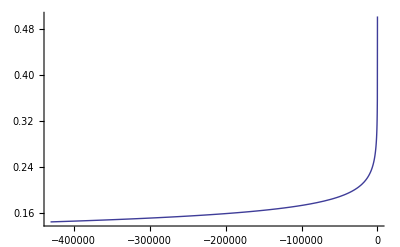

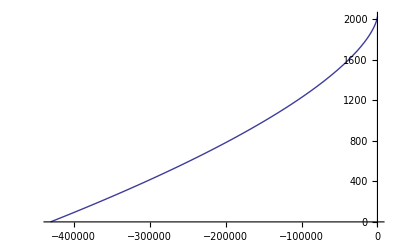

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T1dEdv[t_]:=((32/5 v^9 nu T1dEdvNum)/T1dEdvDen/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T1dEdv[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Print["The plots start at: ", t0-tOffset]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```

## TaylorT2

```mathematica
T2t=Collect[Expand[(256ν v^8)/5∫Normal[Series[E'[v]/((ℱ[v]/.{Log[16 v^2]->Log[16]+2lnv})+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis}},{v,0,-2}]]ⅆv]/.{Log[v]->lnv},v,FullSimplify]/.ν->nu
T2Φ=Collect[Expand[32ν v^5∫Normal[Series[v^3 E'[v]/((ℱ[v]/.{Log[16 v^2]->Log[16]+2lnv})+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis}},{v,0,1}]]ⅆv]/.{Log[v]->lnv},v,FullSimplify]/.ν->nu
```

1+(743/252+(11 nu)/3) v^2-2/15 (chis (-113+76 nu)+48 π) v^3+(3058673/508032+1/8 chis^2 (-81+4 nu)+1/504 nu (5429+4319 nu)) v^4+(chis^3 (4-12 nu)+1/756 chis (147605-112 nu (1240+153 nu))-(7729 π)/252+(13 nu π)/3) v^5+(-1/84 chis^3 (16437+2 nu (-4415+9352 nu))+(chis (4092843763+4 nu (-878933759+252 nu (-2289311+401548 nu))))/1524096+4 chis^2 (57-4 nu) π+((-15419335+168 nu (-75703+29618 nu)) π)/127008) v^7+v^6 (-10817850546611/23471078400+(6848 EulerGamma)/105+(6848 lnv)/105+1/672 chis^2 (6845+4 nu (-43427+13720 nu))+(nu (3147553127+588 nu (-45633+102260 nu)))/3048192+8/3 chis (-73+56 nu) π+1/12 (512-451 nu) π^2+(3424 Log[16])/105)

1+(5 (743+924 nu) v^2)/1008-5/24 (chis (-113+76 nu)+48 π) v^3+(5/16 chis^2 (-81+4 nu)+(5 (3058673+1008 nu (5429+4319 nu)))/1016064) v^4+(5 lnv (3024 chis^3 (-1+3 nu)+chis (-147605+112 nu (1240+153 nu))+3 (7729-1092 nu) π) v^5)/2016+1/24385536 5 (18144 chis^3 (16437+2 nu (-4415+9352 nu))+chis (-4092843763+4 nu (878933759+252 (2289311-401548 nu) nu))+6096384 chis^2 (-57+4 nu) π+12 (15419335+168 (75703-29618 nu) nu) π) v^7+v^6 (10817850546611/18776862720-(1712 EulerGamma)/21-(1712 lnv)/21-(5 chis^2 (6845+4 nu (-43427+13720 nu)))/2688-(5 nu (3147553127+588 nu (-45633+102260 nu)))/12192768+10/3 chis (73-56 nu) π+5/48 (-512+451 nu) π^2-(856 Log[16])/21)

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T2.txt"];
t2=CForm[Collect[SeriesCoefficient[T2t,{v,0,2}],{chis,nu}]];
t3=CForm[Collect[SeriesCoefficient[T2t,{v,0,3}],{chis,nu}]];
t4=CForm[Collect[SeriesCoefficient[T2t,{v,0,4}],{chis,nu}]];
t5=CForm[Collect[SeriesCoefficient[T2t,{v,0,5}],{chis,nu}]];
t6=CForm[Collect[N[SeriesCoefficient[T2t,{v,0,6}]/.lnv->0],{chis,nu}]];
t6Lnv=CForm[Collect[D[SeriesCoefficient[T2t,{v,0,6}],lnv],{chis,nu}]];
t7=CForm[Collect[SeriesCoefficient[T2t,{v,0,7}],{chis,nu}]];
WriteString[OutFile,StringForm["      t2(``),\n", t2]]
WriteString[OutFile,StringForm["      t3(``),\n", t3]]
WriteString[OutFile,StringForm["      t4(``),\n", t4]]
WriteString[OutFile,StringForm["      t5(``),\n", t5]]
WriteString[OutFile,StringForm["      t6(``),\n", t6]]
WriteString[OutFile,StringForm["      t6Lnv(``),\n", t6Lnv]]
WriteString[OutFile,StringForm["      t7(``),\n", t7]]
Phi2=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,2}],{chis,nu}]];
Phi3=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,3}],{chis,nu}]];
Phi4=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,4}],{chis,nu}]];
Phi5Lnv=CForm[Collect[D[SeriesCoefficient[T2Φ,{v,0,5}],lnv],{chis,nu}]];
Phi6=CForm[Collect[N[SeriesCoefficient[T2Φ,{v,0,6}]/.lnv->0],{chis,nu}]];
Phi6Lnv=CForm[Collect[D[SeriesCoefficient[T2Φ,{v,0,6}],lnv],{chis,nu}]];
Phi7=CForm[Collect[SeriesCoefficient[T2Φ,{v,0,7}],{chis,nu}]];
WriteString[OutFile,StringForm["      Phi2(``),\n", Phi2]];
WriteString[OutFile,StringForm["      Phi3(``),\n", Phi3]];
WriteString[OutFile,StringForm["      Phi4(``),\n", Phi4]];
WriteString[OutFile,StringForm["      Phi5Lnv(``),\n", Phi5Lnv]];
WriteString[OutFile,StringForm["      Phi6(``),\n", Phi6]];
WriteString[OutFile,StringForm["      Phi6Lnv(``),\n", Phi6Lnv]];
WriteString[OutFile,StringForm["      Phi7(``)\n"  , Phi7]];
Close[OutFile];
```

The plots start at: -430541.

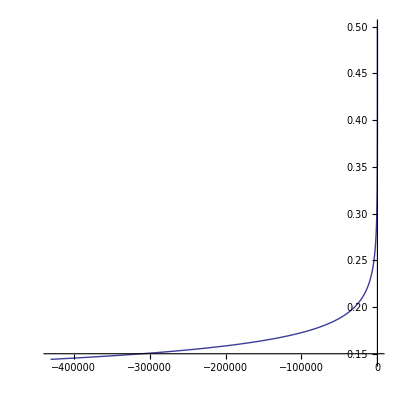

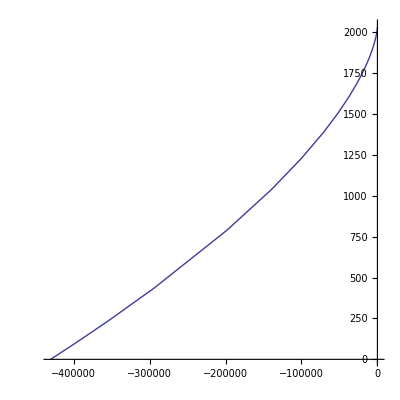

```mathematica
chis=0;
nu=1/4;
v0=0.144;
v1=0.5;
T2tFunc[va_]=(-5/(256nu va^8)T2t/.{v->va,lnv->Log[va]});
T2PhiFunc[va_]=(1/(32nu va^5)T2Φ/.{v->va,lnv->Log[va]});
Print["The plots start at: ",T2tFunc[v0]]
ParametricPlot[{T2tFunc[v],v},{v,v0,v1},AspectRatio->1,PlotRange->All]
ParametricPlot[{T2tFunc[v],T2PhiFunc[v0]-T2PhiFunc[v]},{v,v0,v1},AspectRatio->1,PlotRange->All]
Clear[v0,v1,nu,chis]
```

## TaylorT3

```mathematica
τ[ν_,t_,t0_]:=ν/5(t0-t);
T3vA[τ_]=Assuming[ν>0,Collect[Normal[
InverseSeries[Series[((5/(256ν v^8)Collect[Expand[(256ν v^8)/5∫Normal[Series[E'[v]/((ℱ[v]/.{Log[16 v^2]->1/4( Log[256]- lntau)})+Mdot[v])/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis}},{v,0,-2}]]ⅆv],v,FullSimplify])),{v,0,-1}],T]]/.{T->(5τ/ν)},v,Simplify]];
T3vA[τ_]=Normal[Series[T3vA[T^-8],{T,0,8}]]/.{T->τ^(-1/8),ν->nu};
T3ΦA[τ_]=-Collect[∫Collect[Normal[Series[(5 T3vA[T^-8]^3)/ν,{T,0,10}]]/.{T->τ^(-1/8)},τ]ⅆτ,τ]/.{ν->nu,Log[τ]->lntau};
T3v=Collect[Simplify[2/τToNegativeOne8th T3vA[τToNegativeOne8th^-8],Assumptions->{τToNegativeOne8th>0}],τToNegativeOne8th]
T3Φ=Collect[Simplify[-nu τToNegativeOne8th^5 T3ΦA[τToNegativeOne8th^-8],Assumptions->{τToNegativeOne8th>0}],τToNegativeOne8th]
```

1+((743+924 nu) τToNegativeOne8th^2)/8064-1/480 (chis (-113+76 nu)+48 π) τToNegativeOne8th^3+((4461199+6825672 nu+6145776 nu^2+127008 chis^2 (-81+4 nu)) τToNegativeOne8th^4)/130056192-((30240 chis^3 (-1+3 nu)+chis (-1392091+1436744 nu+101136 nu^2)+6 (32701-12852 nu) π) τToNegativeOne8th^5)/1935360-1/1560674304(18144 chis^3 (16437-8830 nu+18704 nu^2)+chis (-4092843763+3515735036 nu+2307625488 nu^2-404760384 nu^3)+6096384 chis^2 (-57+4 nu) π+12 (15419335+12718104 nu-4975824 nu^2) π) τToNegativeOne8th^7+1/288412611379200 τToNegativeOne8th^6 (-260539947604339+36738273116160 EulerGamma-4592284139520 lntau+579139571772300 nu-7948730235600 nu^2+9550175342400 nu^3+1397088 chis^2 (-108937-94733152 nu+30247952 nu^2)+240343842816 chis (-428+331 nu) π+22592321224704 π^2-21170912716800 nu π^2+36738273116160 Log[2])

1+(5 (743+924 nu) τToNegativeOne8th^2)/8064-1/64 (chis (-113+76 nu)+48 π) τToNegativeOne8th^3+(5 (1855099+3190600 nu+2617776 nu^2+42336 chis^2 (-81+4 nu)) τToNegativeOne8th^4)/14450688-(5 lntau (3024 chis^3 (-1+3 nu)+chis (-147605+138880 nu+17136 nu^2)+3 (7729-1092 nu) π) τToNegativeOne8th^5)/516096+1/520224768(756 chis^3 (1163573-642468 nu+1184064 nu^2)+chis (-10820083342+8611760654 nu+6449430792 nu^2-898680384 nu^3)+2286144 chis^2 (-407+28 nu) π+3 (188516689+164245200 nu-47634384 nu^2) π) τToNegativeOne8th^7+1/57682522275840 τToNegativeOne8th^6 (775925041075117-110214819348480 EulerGamma+13776852418560 lntau-1753429845806100 nu+4858670401200 nu^2-38454265080000 nu^3-4191264 chis^2 (8322937-113716448 nu+35608048 nu^2)-1081547292672 chis (-323+246 nu) π-76429342015488 π^2+63512738150400 nu π^2-110214819348480 Log[2])

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T3.txt"];
v2=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,2}]];
v3=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,3}]];
v4=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,4}]];
v5=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,5}]];
v6=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,6}]/.lntau->0];
v6lntau=CForm[D[SeriesCoefficient[T3v,{τToNegativeOne8th,0,6}],lntau]];
v7=CForm[SeriesCoefficient[T3v,{τToNegativeOne8th,0,7}]];
WriteString[OutFile,StringForm["      v2(``),\n", v2/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v3(``),\n", v3/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v4(``),\n", v4/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v5(``),\n", v5/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v6(``),\n", v6/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v6lntau(``),\n", v6lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      v7(``),\n", v7/.τToNegativeOne8th->taum8]]
Phi2=CForm[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,2}]];
Phi3=CForm[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,3}]];
Phi4=CForm[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,4}]];
Phi5lntau=CForm[D[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,5}],lntau]];
Phi6=CForm[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,6}]/.lntau->0];
Phi6lntau=CForm[D[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,6}],lntau]];
Phi7=CForm[SeriesCoefficient[T3Φ,{τToNegativeOne8th,0,7}]];
WriteString[OutFile,StringForm["      Phi2(``),\n", Phi2/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi3(``),\n", Phi3/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi4(``),\n", Phi4/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi5lntau(``),\n", Phi5lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi6(``),\n", Phi6/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi6lntau(``),\n", Phi6lntau/.τToNegativeOne8th->taum8]]
WriteString[OutFile,StringForm["      Phi7(``)\n", Phi7/.τToNegativeOne8th->taum8]]
Close[OutFile];
```

## TaylorT4

```mathematica
T4dEdv=Collect[5/(32ν v^9)Series[Simplify[-(ℱ[v]+Mdot[v])/D[E[v],v]/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis},Log[16 v^2]->2ln4v}],{v,0,16}],{v,χa,χs,ν},FullSimplify]/.ν->nu
```

1+(-743/336-(11 nu)/4) v^2+(-(113 chis)/12+(19 chis nu)/3+4 π) v^3+(34103/18144+(81 chis^2)/16+(13661/2016-chis^2/4) nu+(59 nu^2)/18) v^4+(-(79 chis nu^2)/3+(-63646 chis-3024 chis^3-12477 π)/2016+nu ((23353 chis)/252+(9 chis^3)/2-(189 π)/8)) v^5+(16447322263/139708800+(128495 chis^2)/2016-(1712 EulerGamma)/105-(1712 ln4v)/105+(541/896+(1517 chis^2)/72) nu^2-(5605 nu^3)/2592-(80 chis π)/3+(16 π^2)/3+nu (-56198689/217728-(23441 chis^2)/288+(40 chis π)/3+(451 π^2)/48)) v^6+(-(2539613 chis)/27216-(257 chis^3)/4+(2045 chis nu^3)/216-(4415 π)/4032+12 chis^2 π+(nu^2 (-1193295 chis-504 chis^3+365980 π))/6048+(nu (10831889 chis+2397276 chis^3+3228075 π))/54432) v^7

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T4.txt"];
dvdt2=CForm[SeriesCoefficient[T4dEdv,{v,0,2}]];
dvdt3=CForm[SeriesCoefficient[T4dEdv,{v,0,3}]];
dvdt4=CForm[SeriesCoefficient[T4dEdv,{v,0,4}]];
dvdt5=CForm[SeriesCoefficient[T4dEdv,{v,0,5}]];
dvdt6=CForm[SeriesCoefficient[T4dEdv,{v,0,6}]/.ln4v->0];
dvdt6Ln4v=CForm[D[SeriesCoefficient[T4dEdv,{v,0,6}],ln4v]];
dvdt7=CForm[SeriesCoefficient[T4dEdv,{v,0,7}]];
WriteString[OutFile,StringForm["      dvdt2(``),\n", dvdt2]]
WriteString[OutFile,StringForm["      dvdt3(``),\n", dvdt3]]
WriteString[OutFile,StringForm["      dvdt4(``),\n", dvdt4]]
WriteString[OutFile,StringForm["      dvdt5(``),\n", dvdt5]]
WriteString[OutFile,StringForm["      dvdt6(``),\n", dvdt6]]
WriteString[OutFile,StringForm["      dvdt6Ln4v(``),\n", dvdt6Ln4v]]
WriteString[OutFile,StringForm["      dvdt7(``)\n", dvdt7]]
Close[OutFile];
```

Stiffness time: -34083.9 (should be less than t1=0.)

The final value of v: 2.08746

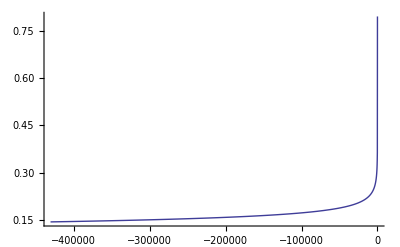

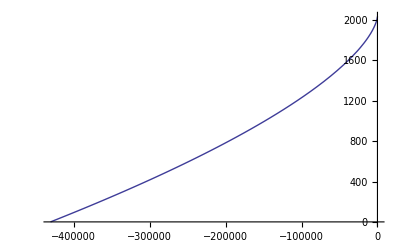

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T4dEdvFunc[t_]:=(32/5 v^9 nu T4dEdv/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T4dEdvFunc[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```